```mathematica
(*Satunnaismuuttujien arvot ovat tasaisille todennäköisyysjakaumille vakioita*)
(*q=tilausmäärä, Z=tilausmäärä,p=hinta, c=hinta per kpl tehtaalle, kysyntä=D, tuotto= p*min(D,Zq)-cZq *) 
ClearAll["Global`*"]
pi[_q] =Integrate[Integrate[d*(300-0)^(-1)*z*(1-0)^(-1)*(p*Min[q*z,d]-c*q*z),{z,0,1}], {d,0,300}]

(*2. ratkaise
Solve[,,Reals]
D
*)
```

Piecewise[{{-50 (c q-p q), q≤0}, {-(50 (5400000 p-300 p q^2+c q^3))/q^2, q>300}, {(-450000 c q+450000 p q-p q^3)/9000, 0<q<300}, {(-5 c q^3+4 p q^3)/9000, True}}]

```mathematica
a[q_] = %6 /. {p->120,c->30}
```

Piecewise[{{4500 q, q≤0}, {-(50 (648000000-36000 q^2+30 q^3))/q^2, q>300}, {(40500000 q-120 q^3)/9000, 0<q<300}, {(11 q^3)/300, True}}]

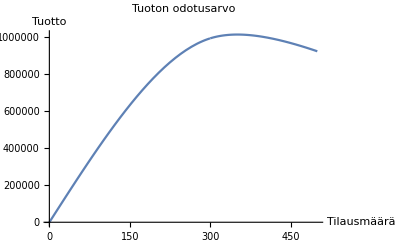

```mathematica
Plot[a[q], {q,0,500}, PlotLabel->"Tuoton odotusarvo", AxesLabel->{"Tilausmäärä", "Tuotto"}]
```

```mathematica
b[q_] = %6;
```

```mathematica
D[b[q],q]
```

Piecewise[{{-50 (c-p), q<0||q==0}, {(-450000 c+450000 p-3 p q^2)/9000, 0<q<300}, {(-450000 c+180000 p)/9000, q==300}, {-(50 (-600 p q+3 c q^2))/q^2+(100 (5400000 p-300 p q^2+c q^3))/q^3, True}}]

```mathematica
c[q_] = %14;
Solve[c[q]==0,q, Reals]
```

```mathematica
{{q->ConditionalExpression[100 √15 √(-(c-p)/p),((2 p)/5<c<p&&p>0)||(p<c<(2 p)/5&&p<0)]},{q->ConditionalExpression[Root[-10800000 p+c #1^3&,1],(0<c<(2 p)/5&&p>0)||((2 p)/5<c<0&&p<0)]}}
d[q_] = %17 /. {p->120,c->30}
```

{{q→ConditionalExpression[100 √15 √(-(c-p)/p),((2 p)/5<c<p&&p>0)||(p<c<(2 p)/5&&p<0)]},{q→ConditionalExpression[Root[-10800000 p+c #1^3&,1],(0<c<(2 p)/5&&p>0)||((2 p)/5<c<0&&p<0)]}}

Piecewise[{{4500, q<0||q==0}, {(40500000-360 q^2)/9000, 0<q<300}, {900, q==300}, {-(50 (-72000 q+90 q^2))/q^2+(100 (648000000-36000 q^2+30 q^3))/q^3, True}}]